import pickle

#### Phase Diagram

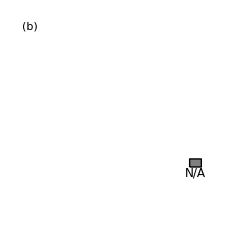
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[ToExpression/@Cases[NotebookRead[NestList[NextCell[#1,CellStyle->"Output"]&,EvaluationCell[],3][[-2;;]]],_BoxData,2],Spacer[2]]
```

```mathematica
Block[{data,fid6,colfunc,mdl,bdy},
data=ExternalEvaluate[First@ExternalSessions[],"pickle.load(open(<*NotebookDirectory[]*>+'/data/map.dat', 'rb'))"];
fid6=ExternalEvaluate[First@ExternalSessions[],"pickle.load(open(<*NotebookDirectory[]*>+'/data/fid6_d128_l2.dat', 'rb'))"];
colfunc=Blend[{{0,Red},{0.3,Orange},{0.35,Yellow},{0.5,Green},{0.65,Cyan},{0.7,LightBlue},{1,Blue}},#]&;
mdl=<|"Atlas"-><|"pos"->{-5,5},"col"->Blue|>,"Boreas"-><|"pos"->{-1,5},"col"->Green|>,"Cygnus"-><|"pos"->{6,5},"col"->Red|>|>;
bdy={Dashed,White,BSplineCurve[{{-6,5.5},{-3.5,5},{-0.5,4},{2,3},{4,2}}],BSplineCurve[{{3,3},{3.5,4},{4.2,5},{5.5,6}}]};
Overlay[{Graphics[{{GrayLevel[1],Rectangle[{0,0},{1,1}]},
Text[Style["(a)",SingleLetterItalics->False],{0,1},{-1.2,1.1}]},
PlotRangePadding->0,AspectRatio->1,ImageSize->240],
Row[{Graphics[{Translate[{EdgeForm[colfunc[#3]],colfunc[#3],Rectangle[{-0.5,-0.5},{0.5,0.5}]},{#1,#2}]&@@@Join[data[[All,{2,1,3}]],{#2,#1,Max[#3]}&@@@fid6],bdy,{White,Text[Style[#1,FontFamily->"CMU Sans Serif"],##2]&@@@{{"Quantum",{-3,2.5}},{"Classical",{1,5.5}},{"Thermal",{5,4},{0,0},{0,-1}}}},Translate[{Arrowheads[0.05],AbsoluteThickness[1],Arrow[{#,0}&/@{-3.5,-6.5}],Text[Style["stronger\nmodel",LineSpacing->{1,0}],{-5,0},{0,0.05}],Arrow[{#,0}&/@{3.5,6.5}],Text[Style["weaker\nmodel",LineSpacing->{1,0}],{5,0},{0,0.05}]},{0,-0.8}],
Table[Translate[{{mdl[name]["col"],Text[name,{-1.4,1.8},{0,-0.7}]},{Lighter[mdl[name]["col"],0.5],{AbsoluteThickness[1],Line[{{0,0},{-1.4,1.8}}],Line[{0.3 StringLength[name]#-1.4,1.8}&/@{-1,1}]},{AbsolutePointSize[5],Point[{0,0}]}}},mdl[name]["pos"]],{name,Keys@mdl}]},BaselinePosition->Scaled[0.584],ImagePadding->{{Automatic,Automatic},{50,25}},Frame->True,FrameLabel->{"\!\(log\_2β\)","qubit number \!\(N\)"},FrameTicks->{{{#,#,{0.015,0}}&/@Range[1,6],{#,Spacer[{0,0}],{0.015,0}}&/@Range[1,6]},{{#,If[EvenQ[#],#,Spacer[{0,0}]],{0.015,0}}&/@Range[-6,6],{#,Spacer[{0,0}],{0.015,0}}&/@Range[-6,6]}},PlotRange->{{-6.5,6.5},{0.5,6.5}},PlotRangeClipping->False,AspectRatio->1,ImageSize->200],Graphics[Raster[List/@Range[0.,1.,0.1],{{0,-0.05},{1,1.05}},ColorFunction->colfunc],PlotLabel->Style["\!\(F\)",14,Black],AspectRatio->8,Frame->True,FrameTicks->{{None,{{0,"0.0"},{0.5,"0.5"},{1,"1.0"}}},{None,None}},ImageSize->{Automatic,140}]}]},Alignment->Center]]
```

-Graphics--Graphics--Graphics-

```mathematica
Block[{data,fid6,colfunc,mdl,bdy},
data=ExternalEvaluate[First@ExternalSessions[],"pickle.load(open(<*NotebookDirectory[]*>+'/data/map.dat', 'rb'))"];
colfunc=Blend[{{0,Blue},{0.8,LightBlue},{1,Green},{2,Blend[{Green,LightGreen}]},{2.5,LightGreen},{3,Yellow},{3.5,Orange},{4,Blend[{Red,Orange}]},{5,Red}},#]&;
mdl=<|"Atlas"-><|"pos"->{-5,5},"col"->Blue|>,"Boreas"-><|"pos"->{-1,5},"col"->Green|>,"Cygnus"-><|"pos"->{6,5},"col"->Red|>|>;
bdy={Dashed,White,BSplineCurve[{{-6,5.5},{-3.5,5},{-0.5,4},{2,3},{4,2}}],BSplineCurve[{{3,3},{3.5,4},{4.2,5},{5.5,6}}]};
Overlay[{Graphics[{{GrayLevel[1],Rectangle[{0,0},{1,1}]},
Translate[Block[{w=0.0298,h=0.0205},{{Gray,Rectangle[{-w,-h},{w,h}]},{AbsoluteThickness[1],Line[{{-w,-h},{-w,h},{w,h},{w,-h},{-w,-h}}]},Text[Style["N/A",12],{0,-h},{-0.3,1}]}],{0.8848,0.281}],
Text[Style["(b)",SingleLetterItalics->False],{0,1},{-1.2,1.1}]},
PlotRangePadding->0,AspectRatio->1,ImageSize->240],
Row[{Graphics[{
{EdgeForm[Gray],Gray,Rectangle[{-6.5,5.5},{6.5,6.5}]},
Translate[{EdgeForm[colfunc[#3]],colfunc[#3],Rectangle[{-0.5,-0.5},{0.5,0.5}]},{#1,#2}]&@@@data[[All,{2,1,4}]],
bdy,{White,Text[Style[#1,FontFamily->"CMU Sans Serif"],##2]&@@@{{"Quantum",{-3,2.5}},{"Classical",{1,5.5}},{"Thermal",{5,4},{0,0},{0,-1}}}},Translate[{Arrowheads[0.05],AbsoluteThickness[1],Arrow[{#,0}&/@{-3.5,-6.5}],Text[Style["stronger\nmodel",LineSpacing->{1,0}],{-5,0},{0,0.05}],Arrow[{#,0}&/@{3.5,6.5}],Text[Style["weaker\nmodel",LineSpacing->{1,0}],{5,0},{0,0.05}]},{0,-0.8}],
Table[Translate[{{mdl[name]["col"],Text[name,{-1.4,1.8},{0,-0.7}]},{Lighter[mdl[name]["col"],0.5],{AbsoluteThickness[1],Line[{{0,0},{-1.4,1.8}}],Line[{0.3 StringLength[name]#-1.4,1.8}&/@{-1,1}]},{AbsolutePointSize[5],Point[{0,0}]}}},mdl[name]["pos"]],{name,Keys@mdl}]},BaselinePosition->Scaled[0.584],ImagePadding->{{Automatic,Automatic},{50,25}},Frame->True,FrameLabel->{"\!\(log\_2β\)","qubit number \!\(N\)"},FrameTicks->{{{#,#,{0.015,0}}&/@Range[1,6],{#,Spacer[{0,0}],{0.015,0}}&/@Range[1,6]},{{#,If[EvenQ[#],#,Spacer[{0,0}]],{0.015,0}}&/@Range[-6,6],{#,Spacer[{0,0}],{0.015,0}}&/@Range[-6,6]}},PlotRange->{{-6.5,6.5},{0.5,6.5}},PlotRangeClipping->False,AspectRatio->1,ImageSize->200],Graphics[Raster[List/@Range[0.,5.,0.5],{{0,-0.25},{1,5.25}},ColorFunction->colfunc],PlotLabel->Style["\!\(S\)",14,Black],AspectRatio->8,Frame->True,FrameTicks->{{None,{#,NumberForm[#,{1,1}]}&/@Range[0,5,1]},{None,None}},ImageSize->{Automatic,140}],Spacer[7]}]},
Alignment->Center]]
```

-Graphics--Graphics--Graphics-

#### Test Analysis

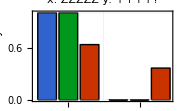
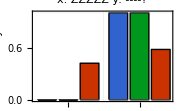
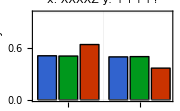
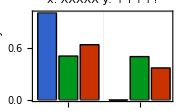
{-Graphics--Graphics--Graphics- | Atlas
-Graphics- | Boreas
-Graphics- | Cygnus,-Graphics--Graphics--Graphics- | Atlas
-Graphics- | Boreas
-Graphics- | Cygnus}

```mathematica
Block[{ztest,xtest,xztest,mdls,cols,legend,chart},
ztest=ExternalEvaluate[First@ExternalSessions[],"pickle.load(open(<*NotebookDirectory[]*>+'/data/z_test.dat', 'rb'))"];
xtest=ExternalEvaluate[First@ExternalSessions[],"pickle.load(open(<*NotebookDirectory[]*>+'/data/x_test.dat', 'rb'))"];
xztest=ExternalEvaluate[First@ExternalSessions[],"pickle.load(open(<*NotebookDirectory[]*>+'/data/xz_test.dat', 'rb'))"];
mdls={"atlas","boreas", "cygnus"};
cols={Blue,Green,Red};
legend=Grid[Thread[{Graphics[{#,EdgeForm[AbsoluteThickness[1]],Rectangle[]},ImageSize->10]&/@cols,Style[Capitalize[#],14,FontFamily->"CMU"]&/@mdls}],Alignment->Left];
chart[test_,v_,prompt_]:=Block[{ind,logit},
ind=Position[test["obs"],{v...}][[1,1]];
logit=test[#][[ind]]&/@mdls;
BarChart[Thread[#/Total[#]&/@Exp[logit]],PlotLabel->Style[prompt,12,LineSpacing->{0,12},FontFamily->"CMU Concrete"],BaselinePosition->Scaled[0.43],GridLines->{{3.9},{0,1}},PlotRange->{0,1},PlotRangePadding->{{0.1,0.2},Scaled[.05]},FrameLabel->{None,"Probability"},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,None}},ChartElementFunction->Function[{region,values,metadata},{EdgeForm[Directive[AbsoluteThickness[1],Black]],Rectangle@@(Thread@region)}],ChartLabels->{{"+","-"},None},ChartStyle->cols,ImageSize->180]];
{Row[{chart[ztest,1,"x: ZZZZZ\ny: ++++?"],chart[ztest,2,"x: ZZZZZ\ny: ----?"],legend},Spacer[0]],
Row[{chart[xztest,1,"x: XXXXZ\ny: ++++?"],chart[xtest,1,"x: XXXXX\ny: ++++?"],legend},Spacer[0]]}]
```

```mathematica
Block[{ztest,mdls,cols,legend,fs,plt},
ztest=ExternalEvaluate[First@ExternalSessions[],"pickle.load(open(<*NotebookDirectory[]*>+'/data/z_test.dat', 'rb'))"];
mdls={"atlas","boreas", "cygnus"};
cols={Blue,Green,Red};
legend=Grid[Thread[{Graphics[{#,EdgeForm[AbsoluteThickness[1]],Rectangle[]},ImageSize->10]&/@cols,Style[Capitalize[#],14,FontFamily->"CMU"]&/@mdls}],Alignment->Left];
fs=Block[{x,ys},
x=Mean/@(ztest["obs"]/.{1->1,2->-1});
ys=Table[#.{1,-1}/Total[#]&/@Exp[ztest[mdl]],{mdl,mdls}];
{Mean[#],MeanDeviation[#]}&/@GroupBy[Thread[{x,#}],First->Last]&/@ys];
plt[mdl_,col_,f_]:={{col,Line[Table[{x,f[x][[1]]},{x,Keys@f}]]},Table[Translate[{{Lighter[col,0.6],AbsoluteThickness[2],Line[{#,-#}&@{0,f[x][[2]]}]},{EdgeForm[col],Lighter[col,0.8],Disk[{0,0},Offset@{2,2}]}},{x,f[x][[1]]}],{x,Keys@f}],{col,Text[Capitalize[mdl],Scaled@{0.06,0.95},{-1,1}]}};
Row[Graphics[#1,GridLines->{Range[-1,1],Range[-1,1]},PlotRange->{-1,1},PlotRangePadding->Scaled[.05],Frame->True,FrameLabel->{"\!\(⟨Z\_\(1:4\)⟩\_observe\)","\!\(⟨Z\_5⟩\_predict\)"},AspectRatio->1,ImageSize->{Automatic,150}]&/@plt@@@Thread[{mdls,cols,fs}]]
]
```

-Graphics--Graphics--Graphics-

#### Density Matrices

```mathematica
Block[{rhos},
rhos=ExternalEvaluate[First@ExternalSessions[],"pickle.load(open(<*NotebookDirectory[]*>+'/data/rhos.dat', 'rb'))"];
Grid@Thread@Table[{Style[Capitalize[mdl],14,<|"atlas"->Blue,"boreas"->Green,"cygnus"->Red|>[mdl],FontFamily->"CMU"],ComplexMatrixPlot[rhos[mdl],Mesh->All,MeshStyle->Directive[AbsoluteThickness[0.5],Opacity[0.2]],FrameTicks->None,ImageSize->128]},{mdl,Keys@rhos}]]
```

Atlas | Boreas | Cygnus
-Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{ztest,xtest,xztest,rhos,mdls,col,phase},
ztest=ExternalEvaluate[First@ExternalSessions[],"pickle.load(open(<*NotebookDirectory[]*>+'/data/z_test.dat', 'rb'))"];
xtest=ExternalEvaluate[First@ExternalSessions[],"pickle.load(open(<*NotebookDirectory[]*>+'/data/x_test.dat', 'rb'))"];
xztest=ExternalEvaluate[First@ExternalSessions[],"pickle.load(open(<*NotebookDirectory[]*>+'/data/xz_test.dat', 'rb'))"];
rhos=ExternalEvaluate[First@ExternalSessions[],"pickle.load(open(<*NotebookDirectory[]*>+'/data/rhos.dat', 'rb'))"];
mdls=Keys@rhos;
col=<|"atlas"->Blue,"boreas"->Green,"cygnus"->Red|>;
phase=<|"atlas"->"Quantum","boreas"->"Classical","cygnus"->"Thermal"|>;
Style[Grid[Thread@Prepend[Table[Block[{rho,matplt,zacc,xacc,fid, ent},
rho=rhos[mdl];
matplt=ComplexMatrixPlot[rho,Epilog->{col[mdl],Text[phase[mdl],Scaled@{0.5,0.5}]},Mesh->All,MeshStyle->Directive[AbsoluteThickness[0.5],Opacity[0.2]],FrameTicks->None,ImageSize->100];
zacc=Tr[#/Total[#]&/@Exp[ztest[mdl][[{1,-1}]]]]/2;
xacc=#[[1]]/Total[#]&@Exp[xtest[mdl][[1]]];
fid=Re[(rho[[1,1]]+rho[[1,-1]]+rho[[-1,1]]+rho[[-1,-1]])/2];
ent=Total[Piecewise[{{-# Log[2,#],#>0},{0,True}}]&/@Ramp[Eigenvalues[rho]]];
{Style[Capitalize[mdl],col[mdl]],NumberForm[zacc,{3,3}],NumberForm[xacc,{3,3}],matplt,NumberForm[fid,{3,3}],NumberForm[ent,{3,3}]}],{mdl,mdls}],
{"Model",Style["\!\(Z\_\(1:4\)→Z\_5\)\naccuracy (↑)",LineSpacing->{0,14}],Style["\!\(X\_\(1:4\)→X\_5\)\naccuracy (↑)",LineSpacing->{0,14}],"\!\(ρ\&~\)","\!\(F(ρ,ρ\&~)\) (↑)","\!\(S(ρ\&~)\) [bit] (↓)"}],
Dividers->{{2->True},{2->True,4->True}}],FontSize->14,SingleLetterItalics->True,FontFamily->"CMU"]]
```

Model | Atlas | Boreas | Cygnus
Z_1:4→Z_5
accuracy (↑) | 1.000 | 1.000 | 0.607
X_1:4→X_5
accuracy (↑) | 1.000 | 0.503 | 0.634
ρ ~ | -Graphics- | -Graphics- | -Graphics-
F(ρ,ρ ~) (↑) | 1.000 | 0.500 | 0.063
S(ρ ~) [bit] (↓) | 0.206 | 1.190 | 4.410

#### Latent Space

```mathematica
Block[{data,mdls,scheme,mark,seed,colfunc,visualize},
data=ExternalEvaluate[First@ExternalSessions[],"pickle.load(open(<*NotebookDirectory[]*>+'/data/z_embed.dat', 'rb'))"];
mdls={"atlas","boreas", "cygnus"};
scheme=<|
"atlas"->Function[{x},Block[{zloc},zloc=Flatten@Position[x,3];
If[zloc==={},Count[x,1],zloc]]],"boreas"->Function[{x},Flatten@Position[x,3]],
"cygnus"->Function[{x},{First@x,Last@x}]|>;
mark=<|"atlas"->{{1,1,1,1,1},{2,2,2,2,2},{1,1,2,2,2},{1,1,1,2,2},{3,1,1,1,1},{1,3,3,1,1},{1,3,1,3,3},{3,1,3,3,3},{3,3,3,3,3}},
"boreas"->{{1,1,1,1,1},{2,2,2,2,2},{1,1,3,1,1},{1,3,1,1,1},{1,1,3,3,1},{1,3,3,1,1},{3,1,1,3,3},{3,1,3,3,3},{1,3,3,3,3},{3,3,3,3,3}},
"cygnus"->{{3,2,3,1,3},{3,2,2,2,3},{3,3,3,3,3},{1,3,3,3,2},{1,3,2,3,2},{1,2,3,2,2}}|>;
seed=<|"atlas"->6,"boreas"->19,"cygnus"->17|>;
colfunc[{a_,b_,c_}]:=Blend[{Cyan,Magenta,Yellow},{a,b,c}];
visualize[mdl_]:=Block[{co,cplt,plt,pdat,mks,bg},
co=AssociationThread[data["x"]->
Block[{frac=0.8,x1,x2,y1,y2,xc,yc},
{{x1,x2},{y1,y2}}=MinMax/@Thread@data[mdl];
{xc,yc}={x1+x2,y1+y2}/2;
{frac(#1-xc)/(x2-x1)+1/2,frac(#2-yc)/(y2-y1)+1/2}&@@@data[mdl]]];
cplt[xs_]:=Block[{a=0.025,ps,p0,r},
ps=co/@xs;
p0=Mean[ps];
r=Max[Norm[#-p0]&/@ps];
r=Sqrt[r^2+a^2];
{{AbsoluteThickness[0.8],Opacity[0.5],White,Sow[{p0,r}];Circle[p0,r]},{colfunc[Table[Count[#1,a],{a,3}]/5],Point[#2]}&@@@Thread[{xs,ps}]}];
{plt,{pdat}}=Reap[cplt/@GatherBy[data["x"],scheme[mdl]]];
mks=Block[{xms,pms,F,rms,F0,sol},
xms=mark[mdl];
pms=co/@xms;
F[rs_List]:=Block[{a=0.025},
{0.05,0.02,1,3}.{Mean[1/Sqrt[Norm[#2-#1[[1]]]^2+#1[[2]]^2]&@@@Tuples[{pdat,rs}]],
Mean[1/Sqrt[Norm[#1-#2]^2+a^2]&@@@Subsets[rs,{2}]], Mean[Norm[#]^2&/@(rs-pms)],
Mean[(Flatten@rs-0.5)^4]}];
SeedRandom[seed[mdl]];
{F0,sol}=FindMinimum[F[rms],{rms,RandomReal[{0,1},Dimensions[pms]]}];
{{White,AbsoluteThickness[0.8],Line[{#2,#3}]},Text[Style[#1,10,FontFamily->"CMU Bright",Background->Black],#3]}&@@@Thread[{Row/@(xms/.{1->Style["X",colfunc[{1,0,0}]],2->Style["Y",colfunc[{0,1,0}]],3->Style["Z",colfunc[{0,0,1}]]}),pms,rms/.sol}]];
bg={{Black,Rectangle[{0,0},{1,1}]},Translate[{White,AbsoluteThickness[1],Line[Offset/@{{0,0},{12,0}}],Line[Offset/@{{0,0},{0,12}}],Text[Style["\!\(z\)",Bold],{0,0},{-1.2,-0.7}]},{0.025,0.025}],
{White,Text[StringTemplate["`1` clusters "][Length[plt]],Scaled@{1,0},{1,-1}]}};
Graphics[{bg,mks,plt},PlotRange->All,PlotRangePadding->0,Frame->True,FrameTicks->None,PlotLabel->Style[Capitalize[mdl],16,<|"atlas"->Blue,"boreas"->Green,"cygnus"->Red|>[mdl]],ImageSize->200]
];
Row[visualize/@mdls,Spacer[1]]
]
```

-Graphics--Graphics--Graphics-